## Set your path to NonLinearSolver and get it

```mathematica
dddRicardo="/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/NonLinearSolver.m";
```

```mathematica
Get[dddRicardo]
```

### DataToEquations and the critical congestion solver

```mathematica
Data=<|"Vertices List"->{1,2,3,4,5,6,7,8,9},"Adjacency Matrix"->{{0,0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,0},{0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,1,1,1},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}},"Entrance Vertices and Currents"->{{1,I1},{2,I2}},"Exit Vertices and Terminal Costs"->{{7,U1},{8,U2},{9,U3}},"Switching Costs"->{{5,6,7,1},{5,6,8,1},{5,6,9,1},{7,6,5,1},{7,6,8,1},{7,6,9,1},{8,6,5,1},{8,6,7,1},{8,6,9,1},{9,6,5,1},{9,6,7,1},{9,6,8,1}}|>;
crit=CriticalCongestionSolver[d2e = Data2Equations[Data/.{I1->200,I2->200,U1->0,U2->0, U3->0}]];//AbsoluteTiming
```

Iterative boolean convert took 0.026049 seconds to terminate

Iterative boolean convert took 4.×10^-6 seconds to terminate

{0.098587,Null}

Don’t worry about the last 3 printed terms when checking for the critical congestion case.

```mathematica
IsNonLinearSolution[crit]@crit["AssoCritical"]
```

EqEntryIn: j24==200&&j26==200	True

EqValueAuxiliaryEdges: u23==u24&&u25==u26&&u17==u18&&u19==u20&&u21==u22	True

EqCompCon: (jt1==0||1000000-u1+u24==0)&&(jt2==0||u1-u24==0)&&(jt3==0||1000000+u26-u3==0)&&(jt4==0||-u26+u3==0)&&(jt5==0||-u2+u4==0)&&(jt6==0||-u2+u5==0)&&(jt7==0||u2-u4==0)&&(jt8==0||-u4+u5==0)&&(jt9==0||u2-u5==0)&&(jt10==0||u4-u5==0)&&(jt11==0||-u6+u7==0)&&(jt12==0||u6-u7==0)&&(jt13==0||-u8+u9==0)&&(jt14==0||u8-u9==0)&&(jt15==0||1-u10+u11==0)&&(jt16==0||1-u10+u13==0)&&(jt17==0||1-u10+u15==0)&&(jt18==0||1+u10-u11==0)&&(jt19==0||1-u11+u13==0)&&(jt20==0||1-u11+u15==0)&&(jt21==0||1+u10-u13==0)&&(jt22==0||1+u11-u13==0)&&(jt23==0||1-u13+u15==0)&&(jt24==0||1+u10-u15==0)&&(jt25==0||1+u11-u15==0)&&(jt26==0||1+u13-u15==0)&&(jt27==0||-u12+u17==0)&&(jt28==0||1000000+u12-u17==0)&&(jt29==0||-u14+u19==0)&&(jt30==0||1000000+u14-u19==0)&&(jt31==0||-u16+u21==0)&&(jt32==0||1000000+u16-u21==0)	True

EqBalanceSplittingCurrents: j1==jt1&&j24==jt2&&j3==jt3&&j26==jt4&&j2==jt5+jt6&&j4==jt7+jt8&&j5==jt10+jt9&&j6==jt11&&j7==jt12&&j8==jt13&&j9==jt14&&j10==jt15+jt16+jt17&&j11==jt18+jt19+jt20&&j13==jt21+jt22+jt23&&j15==jt24+jt25+jt26&&j12==jt27&&j17==jt28&&j14==jt29&&j19==jt30&&j16==jt31&&j21==jt32	True

EqCurrentCompCon: (j1==0||j2==0)&&(j3==0||j4==0)&&(j5==0||j6==0)&&(j7==0||j8==0)&&(j9==0||j10==0)&&(j11==0||j12==0)&&(j13==0||j14==0)&&(j15==0||j16==0)&&(j17==0||j18==0)&&(j19==0||j20==0)&&(j21==0||j22==0)&&(j23==0||j24==0)&&(j25==0||j26==0)	True

EqTransitionCompCon: (jt1==0||jt2==0)&&(jt10==0||jt8==0)&&(jt11==0||jt12==0)&&(jt13==0||jt14==0)&&(jt15==0||jt18==0)&&(jt16==0||jt21==0)&&(jt17==0||jt24==0)&&(jt19==0||jt22==0)&&(jt20==0||jt25==0)&&(jt23==0||jt26==0)&&(jt27==0||jt28==0)&&(jt29==0||jt30==0)&&(jt3==0||jt4==0)&&(jt31==0||jt32==0)&&(jt5==0||jt7==0)&&(jt6==0||jt9==0)	True

EqPosJs: j1≥0&&j2≥0&&j3≥0&&j4≥0&&j5≥0&&j6≥0&&j7≥0&&j8≥0&&j9≥0&&j10≥0&&j11≥0&&j12≥0&&j13≥0&&j14≥0&&j15≥0&&j16≥0&&j17≥0&&j18≥0&&j19≥0&&j20≥0&&j21≥0&&j22≥0&&j23≥0&&j24≥0&&j25≥0&&j26≥0	True

EqPosJts: jt1≥0&&jt2≥0&&jt3≥0&&jt4≥0&&jt5≥0&&jt6≥0&&jt7≥0&&jt8≥0&&jt9≥0&&jt10≥0&&jt11≥0&&jt12≥0&&jt13≥0&&jt14≥0&&jt15≥0&&jt16≥0&&jt17≥0&&jt18≥0&&jt19≥0&&jt20≥0&&jt21≥0&&jt22≥0&&jt23≥0&&jt24≥0&&jt25≥0&&jt26≥0&&jt27≥0&&jt28≥0&&jt29≥0&&jt30≥0&&jt31≥0&&jt32≥0	True

EqSwitchingByVertex: u1≤1000000+u24&&u24≤u1&&u3≤1000000+u26&&u26≤u3&&u2≤u4&&u2≤u5&&u4≤u2&&u4≤u5&&u5≤u2&&u5≤u4&&u6≤u7&&u7≤u6&&u8≤u9&&u9≤u8&&u10≤1+u11&&u10≤1+u13&&u10≤1+u15&&u11≤1+u10&&u11≤1+u13&&u11≤1+u15&&u13≤1+u10&&u13≤1+u11&&u13≤1+u15&&u15≤1+u10&&u15≤1+u11&&u15≤1+u13&&u12≤u17&&u17≤1000000+u12&&u14≤u19&&u19≤1000000+u14&&u16≤u21&&u21≤1000000+u16	True

Nlhs: {-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16}	{0.,0.,0.,0.,0.,0.,0.,0.}

Nrhs: {-j1+j2-IntM[-j1+j2,1->3],-j3+j4-IntM[-j3+j4,2->3],-j5+j6-IntM[-j5+j6,3->4],-j7+j8-IntM[-j7+j8,4->5],j10-j9-IntM[j10-j9,5->6],-j11+j12-IntM[-j11+j12,6->7],-j13+j14-IntM[-j13+j14,6->8],-j15+j16-IntM[-j15+j16,6->9]}	{-401.066,-401.066,-1002.32,-1002.32,-1002.32,-232.851,-232.851,-232.851}

Max error for non-linear solution: 1002.32

<|j24→200,j26→200,j23→0,j25→0,j17→0,j19→0,j21→0,j2→200,j4→200,j1→0,j3→0,j6→400,j5→0,j8→400,j7→0,j10→400,j9→0,j12→400/3,j14→400/3,j16→400/3,j11→0,j18→400/3,j13→0,j20→400/3,j15→0,j22→400/3,u18→0,u20→0,u22→0,jt11→400,jt12→0,jt17→400/3,jt2→200,jt20→0,jt21→0,jt23→0,jt26→0,jt27→400/3,jt28→0,jt29→400/3,jt3→0,jt30→0,jt31→400/3,jt32→0,jt4→200,jt5→0,jt6→200,jt7→0,jt8→200,jt9→0,u17→0,u19→0,u21→0,u24→4603/3,u26→4603/3,jt1→0,jt10→0,jt13→400,jt14→0,jt18→0,jt19→0,jt22→0,jt24→0,jt25→0,u2→4003/3,u23→4603/3,u3→4603/3,u5→4003/3,u7→2803/3,u9→1603/3,u1→4603/3,u12→0,u14→0,u16→0,u25→4603/3,u4→4003/3,u6→2803/3,u8→1603/3,jt15→400/3,jt16→400/3,u10→403/3,u11→400/3,u13→400/3,u15→400/3|>

#### Non-critical congestion solver

#### Starting from the critical congestion solution

```mathematica
nn=NonLinear[crit];//AbsoluteTiming
IsNonLinearSolution[nn][nn["AssoNonCritical"]];
```

Iterative boolean convert took 0.022937 seconds to terminate

Iterative boolean convert took 5.×10^-6 seconds to terminate

Iterative boolean convert took 0.022367 seconds to terminate

Iterative boolean convert took 5.×10^-6 seconds to terminate

Iterated 2 times out of 15

{0.163812,Null}

EqEntryIn: j24==200&&j26==200	True

EqValueAuxiliaryEdges: u23==u24&&u25==u26&&u17==u18&&u19==u20&&u21==u22	True

EqCompCon: (jt1==0||1000000-u1+u24==0)&&(jt2==0||u1-u24==0)&&(jt3==0||1000000+u26-u3==0)&&(jt4==0||-u26+u3==0)&&(jt5==0||-u2+u4==0)&&(jt6==0||-u2+u5==0)&&(jt7==0||u2-u4==0)&&(jt8==0||-u4+u5==0)&&(jt9==0||u2-u5==0)&&(jt10==0||u4-u5==0)&&(jt11==0||-u6+u7==0)&&(jt12==0||u6-u7==0)&&(jt13==0||-u8+u9==0)&&(jt14==0||u8-u9==0)&&(jt15==0||1-u10+u11==0)&&(jt16==0||1-u10+u13==0)&&(jt17==0||1-u10+u15==0)&&(jt18==0||1+u10-u11==0)&&(jt19==0||1-u11+u13==0)&&(jt20==0||1-u11+u15==0)&&(jt21==0||1+u10-u13==0)&&(jt22==0||1+u11-u13==0)&&(jt23==0||1-u13+u15==0)&&(jt24==0||1+u10-u15==0)&&(jt25==0||1+u11-u15==0)&&(jt26==0||1+u13-u15==0)&&(jt27==0||-u12+u17==0)&&(jt28==0||1000000+u12-u17==0)&&(jt29==0||-u14+u19==0)&&(jt30==0||1000000+u14-u19==0)&&(jt31==0||-u16+u21==0)&&(jt32==0||1000000+u16-u21==0)	True

EqBalanceSplittingCurrents: j1==jt1&&j24==jt2&&j3==jt3&&j26==jt4&&j2==jt5+jt6&&j4==jt7+jt8&&j5==jt10+jt9&&j6==jt11&&j7==jt12&&j8==jt13&&j9==jt14&&j10==jt15+jt16+jt17&&j11==jt18+jt19+jt20&&j13==jt21+jt22+jt23&&j15==jt24+jt25+jt26&&j12==jt27&&j17==jt28&&j14==jt29&&j19==jt30&&j16==jt31&&j21==jt32	True

EqCurrentCompCon: (j1==0||j2==0)&&(j3==0||j4==0)&&(j5==0||j6==0)&&(j7==0||j8==0)&&(j9==0||j10==0)&&(j11==0||j12==0)&&(j13==0||j14==0)&&(j15==0||j16==0)&&(j17==0||j18==0)&&(j19==0||j20==0)&&(j21==0||j22==0)&&(j23==0||j24==0)&&(j25==0||j26==0)	True

EqTransitionCompCon: (jt1==0||jt2==0)&&(jt10==0||jt8==0)&&(jt11==0||jt12==0)&&(jt13==0||jt14==0)&&(jt15==0||jt18==0)&&(jt16==0||jt21==0)&&(jt17==0||jt24==0)&&(jt19==0||jt22==0)&&(jt20==0||jt25==0)&&(jt23==0||jt26==0)&&(jt27==0||jt28==0)&&(jt29==0||jt30==0)&&(jt3==0||jt4==0)&&(jt31==0||jt32==0)&&(jt5==0||jt7==0)&&(jt6==0||jt9==0)	True

EqPosJs: j1≥0&&j2≥0&&j3≥0&&j4≥0&&j5≥0&&j6≥0&&j7≥0&&j8≥0&&j9≥0&&j10≥0&&j11≥0&&j12≥0&&j13≥0&&j14≥0&&j15≥0&&j16≥0&&j17≥0&&j18≥0&&j19≥0&&j20≥0&&j21≥0&&j22≥0&&j23≥0&&j24≥0&&j25≥0&&j26≥0	True

EqPosJts: jt1≥0&&jt2≥0&&jt3≥0&&jt4≥0&&jt5≥0&&jt6≥0&&jt7≥0&&jt8≥0&&jt9≥0&&jt10≥0&&jt11≥0&&jt12≥0&&jt13≥0&&jt14≥0&&jt15≥0&&jt16≥0&&jt17≥0&&jt18≥0&&jt19≥0&&jt20≥0&&jt21≥0&&jt22≥0&&jt23≥0&&jt24≥0&&jt25≥0&&jt26≥0&&jt27≥0&&jt28≥0&&jt29≥0&&jt30≥0&&jt31≥0&&jt32≥0	True

EqSwitchingByVertex: u1≤1000000+u24&&u24≤u1&&u3≤1000000+u26&&u26≤u3&&u2≤u4&&u2≤u5&&u4≤u2&&u4≤u5&&u5≤u2&&u5≤u4&&u6≤u7&&u7≤u6&&u8≤u9&&u9≤u8&&u10≤1+u11&&u10≤1+u13&&u10≤1+u15&&u11≤1+u10&&u11≤1+u13&&u11≤1+u15&&u13≤1+u10&&u13≤1+u11&&u13≤1+u15&&u15≤1+u10&&u15≤1+u11&&u15≤1+u13&&u12≤u17&&u17≤1000000+u12&&u14≤u19&&u19≤1000000+u14&&u16≤u21&&u21≤1000000+u16	True

Nlhs: {-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16}	{-401.066,-401.066,-1002.32,-1002.32,-1002.32,-232.851,-232.851,-232.851}

Nrhs: {-j1+j2-IntM[-j1+j2,1->3],-j3+j4-IntM[-j3+j4,2->3],-j5+j6-IntM[-j5+j6,3->4],-j7+j8-IntM[-j7+j8,4->5],j10-j9-IntM[j10-j9,5->6],-j11+j12-IntM[-j11+j12,6->7],-j13+j14-IntM[-j13+j14,6->8],-j15+j16-IntM[-j15+j16,6->9]}	{-401.066,-401.066,-1002.32,-1002.32,-1002.32,-232.851,-232.851,-232.851}

Max error for non-linear solution: 4.54747×10^-13

#### Starting from the zero cpc’s

```mathematica
Get[dddRicardo]
nn=NonLinear[d2e];//AbsoluteTiming
IsNonLinearSolution[nn][nn["AssoNonCritical"]];
```

Iterative boolean convert took 0.024676 seconds to terminate

Iterative boolean convert took 5.×10^-6 seconds to terminate

Iterative boolean convert took 0.053094 seconds to terminate

Iterative boolean convert took 5.×10^-6 seconds to terminate

Iterative boolean convert took 0.023074 seconds to terminate

Iterative boolean convert took 6.×10^-6 seconds to terminate

Iterated 3 times out of 15

{0.253504,Null}

EqEntryIn: j24==200&&j26==200	True

EqValueAuxiliaryEdges: u23==u24&&u25==u26&&u17==u18&&u19==u20&&u21==u22	True

EqCompCon: (jt1==0||1000000-u1+u24==0)&&(jt2==0||u1-u24==0)&&(jt3==0||1000000+u26-u3==0)&&(jt4==0||-u26+u3==0)&&(jt5==0||-u2+u4==0)&&(jt6==0||-u2+u5==0)&&(jt7==0||u2-u4==0)&&(jt8==0||-u4+u5==0)&&(jt9==0||u2-u5==0)&&(jt10==0||u4-u5==0)&&(jt11==0||-u6+u7==0)&&(jt12==0||u6-u7==0)&&(jt13==0||-u8+u9==0)&&(jt14==0||u8-u9==0)&&(jt15==0||1-u10+u11==0)&&(jt16==0||1-u10+u13==0)&&(jt17==0||1-u10+u15==0)&&(jt18==0||1+u10-u11==0)&&(jt19==0||1-u11+u13==0)&&(jt20==0||1-u11+u15==0)&&(jt21==0||1+u10-u13==0)&&(jt22==0||1+u11-u13==0)&&(jt23==0||1-u13+u15==0)&&(jt24==0||1+u10-u15==0)&&(jt25==0||1+u11-u15==0)&&(jt26==0||1+u13-u15==0)&&(jt27==0||-u12+u17==0)&&(jt28==0||1000000+u12-u17==0)&&(jt29==0||-u14+u19==0)&&(jt30==0||1000000+u14-u19==0)&&(jt31==0||-u16+u21==0)&&(jt32==0||1000000+u16-u21==0)	True

EqBalanceSplittingCurrents: j1==jt1&&j24==jt2&&j3==jt3&&j26==jt4&&j2==jt5+jt6&&j4==jt7+jt8&&j5==jt10+jt9&&j6==jt11&&j7==jt12&&j8==jt13&&j9==jt14&&j10==jt15+jt16+jt17&&j11==jt18+jt19+jt20&&j13==jt21+jt22+jt23&&j15==jt24+jt25+jt26&&j12==jt27&&j17==jt28&&j14==jt29&&j19==jt30&&j16==jt31&&j21==jt32	True

EqCurrentCompCon: (j1==0||j2==0)&&(j3==0||j4==0)&&(j5==0||j6==0)&&(j7==0||j8==0)&&(j9==0||j10==0)&&(j11==0||j12==0)&&(j13==0||j14==0)&&(j15==0||j16==0)&&(j17==0||j18==0)&&(j19==0||j20==0)&&(j21==0||j22==0)&&(j23==0||j24==0)&&(j25==0||j26==0)	True

EqTransitionCompCon: (jt1==0||jt2==0)&&(jt10==0||jt8==0)&&(jt11==0||jt12==0)&&(jt13==0||jt14==0)&&(jt15==0||jt18==0)&&(jt16==0||jt21==0)&&(jt17==0||jt24==0)&&(jt19==0||jt22==0)&&(jt20==0||jt25==0)&&(jt23==0||jt26==0)&&(jt27==0||jt28==0)&&(jt29==0||jt30==0)&&(jt3==0||jt4==0)&&(jt31==0||jt32==0)&&(jt5==0||jt7==0)&&(jt6==0||jt9==0)	True

EqPosJs: j1≥0&&j2≥0&&j3≥0&&j4≥0&&j5≥0&&j6≥0&&j7≥0&&j8≥0&&j9≥0&&j10≥0&&j11≥0&&j12≥0&&j13≥0&&j14≥0&&j15≥0&&j16≥0&&j17≥0&&j18≥0&&j19≥0&&j20≥0&&j21≥0&&j22≥0&&j23≥0&&j24≥0&&j25≥0&&j26≥0	True

EqPosJts: jt1≥0&&jt2≥0&&jt3≥0&&jt4≥0&&jt5≥0&&jt6≥0&&jt7≥0&&jt8≥0&&jt9≥0&&jt10≥0&&jt11≥0&&jt12≥0&&jt13≥0&&jt14≥0&&jt15≥0&&jt16≥0&&jt17≥0&&jt18≥0&&jt19≥0&&jt20≥0&&jt21≥0&&jt22≥0&&jt23≥0&&jt24≥0&&jt25≥0&&jt26≥0&&jt27≥0&&jt28≥0&&jt29≥0&&jt30≥0&&jt31≥0&&jt32≥0	True

EqSwitchingByVertex: u1≤1000000+u24&&u24≤u1&&u3≤1000000+u26&&u26≤u3&&u2≤u4&&u2≤u5&&u4≤u2&&u4≤u5&&u5≤u2&&u5≤u4&&u6≤u7&&u7≤u6&&u8≤u9&&u9≤u8&&u10≤1+u11&&u10≤1+u13&&u10≤1+u15&&u11≤1+u10&&u11≤1+u13&&u11≤1+u15&&u13≤1+u10&&u13≤1+u11&&u13≤1+u15&&u15≤1+u10&&u15≤1+u11&&u15≤1+u13&&u12≤u17&&u17≤1000000+u12&&u14≤u19&&u19≤1000000+u14&&u16≤u21&&u21≤1000000+u16	True

Nlhs: {-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16}	{-401.066,-401.066,-1002.32,-1002.32,-1002.32,-232.851,-232.851,-232.851}

Nrhs: {-j1+j2-IntM[-j1+j2,1->3],-j3+j4-IntM[-j3+j4,2->3],-j5+j6-IntM[-j5+j6,3->4],-j7+j8-IntM[-j7+j8,4->5],j10-j9-IntM[j10-j9,5->6],-j11+j12-IntM[-j11+j12,6->7],-j13+j14-IntM[-j13+j14,6->8],-j15+j16-IntM[-j15+j16,6->9]}	{-401.066,-401.066,-1002.32,-1002.32,-1002.32,-232.851,-232.851,-232.851}

Max error for non-linear solution: 1.13687×10^-13

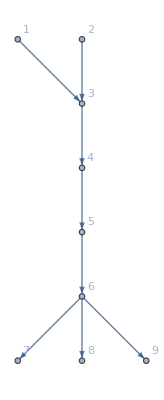
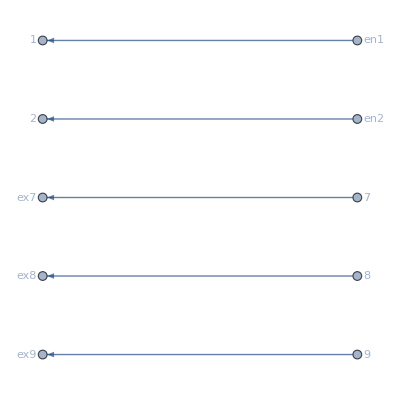
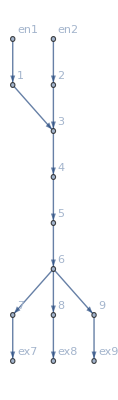
<|Vertices List→{1,2,3,4,5,6,7,8,9},Adjacency Matrix→{{0,0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,0},{0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,1,1,1},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}},Entrance Vertices and Currents→{{1,200},{2,200}},Exit Vertices and Terminal Costs→{{7,0},{8,0},{9,0}},Switching Costs→{{5,6,7,1},{5,6,8,1},{5,6,9,1},{7,6,5,1},{7,6,8,1},{7,6,9,1},{8,6,5,1},{8,6,7,1},{8,6,9,1},{9,6,5,1},{9,6,7,1},{9,6,8,1}},VL→{1,2,3,4,5,6,7,8,9},AM→{{0,0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,0},{0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,1,1,1},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}},EVC→{{1,200},{2,200}},EVTC→{{7,0},{8,0},{9,0}},SC→{{5,6,7,1},{5,6,8,1},{5,6,9,1},{7,6,5,1},{7,6,8,1},{7,6,9,1},{8,6,5,1},{8,6,7,1},{8,6,9,1},{9,6,5,1},{9,6,7,1},{9,6,8,1}},BG→-Graphics-,EntranceVertices→{1,2},InwardVertices→<|1→en1,2→en2|>,ExitVertices→{7,8,9},OutwardVertices→<|7→ex7,8→ex8,9→ex9|>,InEdges→{en1->1,en2->2},OutEdges→{7->ex7,8->ex8,9->ex9},AuxiliaryGraph→-Graphics-,FG→-Graphics-,EL→{1->3,2->3,3->4,4->5,5->6,6->7,6->8,6->9,7->ex7,8->ex8,9->ex9,en1->1,en2->2},BEL→{1->3,2->3,3->4,4->5,5->6,6->7,6->8,6->9},FVL→{1,2,3,4,5,6,7,8,9,en1,en2,ex7,ex8,ex9},jargs→{{1,1->3},{3,1->3},{2,2->3},{3,2->3},{3,3->4},{4,3->4},{4,4->5},{5,4->5},{5,5->6},{6,5->6},{6,6->7},{7,6->7},{6,6->8},{8,6->8},{6,6->9},{9,6->9},{7,7->ex7},{ex7,7->ex7},{8,8->ex8},{ex8,8->ex8},{9,9->ex9},{ex9,9->ex9},{en1,en1->1},{1,en1->1},{en2,en2->2},{2,en2->2}},uargs→{{1,1->3},{3,1->3},{2,2->3},{3,2->3},{3,3->4},{4,3->4},{4,4->5},{5,4->5},{5,5->6},{6,5->6},{6,6->7},{7,6->7},{6,6->8},{8,6->8},{6,6->9},{9,6->9},{7,7->ex7},{ex7,7->ex7},{8,8->ex8},{ex8,8->ex8},{9,9->ex9},{ex9,9->ex9},{en1,en1->1},{1,en1->1},{en2,en2->2},{2,en2->2}},AllTransitions→{{1,1->3,en1->1},{1,en1->1,1->3},{2,2->3,en2->2},{2,en2->2,2->3},{3,1->3,2->3},{3,1->3,3->4},{3,2->3,1->3},{3,2->3,3->4},{3,3->4,1->3},{3,3->4,2->3},{4,3->4,4->5},{4,4->5,3->4},{5,4->5,5->6},{5,5->6,4->5},{6,5->6,6->7},{6,5->6,6->8},{6,5->6,6->9},{6,6->7,5->6},{6,6->7,6->8},{6,6->7,6->9},{6,6->8,5->6},{6,6->8,6->7},{6,6->8,6->9},{6,6->9,5->6},{6,6->9,6->7},{6,6->9,6->8},{7,6->7,7->ex7},{7,7->ex7,6->7},{8,6->8,8->ex8},{8,8->ex8,6->8},{9,6->9,9->ex9},{9,9->ex9,6->9}},EntryArgs→{{1,en1->1},{2,en2->2}},EntryDataAssociation→<|{1,en1->1}→200,{2,en2->2}→200|>,ExitCosts→<|ex7→0,ex8→0,ex9→0|>,js→{j1,j2,j3,j4,j5,j6,j7,j8,j9,j10,j11,j12,j13,j14,j15,j16,j17,j18,j19,j20,j21,j22,j23,j24,j25,j26},jvars→<|{1,1->3}→j1,{3,1->3}→j2,{2,2->3}→j3,{3,2->3}→j4,{3,3->4}→j5,{4,3->4}→j6,{4,4->5}→j7,{5,4->5}→j8,{5,5->6}→j9,{6,5->6}→j10,{6,6->7}→j11,{7,6->7}→j12,{6,6->8}→j13,{8,6->8}→j14,{6,6->9}→j15,{9,6->9}→j16,{7,7->ex7}→j17,{ex7,7->ex7}→j18,{8,8->ex8}→j19,{ex8,8->ex8}→j20,{9,9->ex9}→j21,{ex9,9->ex9}→j22,{en1,en1->1}→j23,{1,en1->1}→j24,{en2,en2->2}→j25,{2,en2->2}→j26|>,us→{u1,u2,u3,u4,u5,u6,u7,u8,u9,u10,u11,u12,u13,u14,u15,u16,u17,u18,u19,u20,u21,u22,u23,u24,u25,u26},uvars→<|{1,1->3}→u1,{3,1->3}→u2,{2,2->3}→u3,{3,2->3}→u4,{3,3->4}→u5,{4,3->4}→u6,{4,4->5}→u7,{5,4->5}→u8,{5,5->6}→u9,{6,5->6}→u10,{6,6->7}→u11,{7,6->7}→u12,{6,6->8}→u13,{8,6->8}→u14,{6,6->9}→u15,{9,6->9}→u16,{7,7->ex7}→u17,{ex7,7->ex7}→u18,{8,8->ex8}→u19,{ex8,8->ex8}→u20,{9,9->ex9}→u21,{ex9,9->ex9}→u22,{en1,en1->1}→u23,{1,en1->1}→u24,{en2,en2->2}→u25,{2,en2->2}→u26|>,jts→{jt1,jt2,jt3,jt4,jt5,jt6,jt7,jt8,jt9,jt10,jt11,jt12,jt13,jt14,jt15,jt16,jt17,jt18,jt19,jt20,jt21,jt22,jt23,jt24,jt25,jt26,jt27,jt28,jt29,jt30,jt31,jt32},jtvars→<|{1,1->3,en1->1}→jt1,{1,en1->1,1->3}→jt2,{2,2->3,en2->2}→jt3,{2,en2->2,2->3}→jt4,{3,1->3,2->3}→jt5,{3,1->3,3->4}→jt6,{3,2->3,1->3}→jt7,{3,2->3,3->4}→jt8,{3,3->4,1->3}→jt9,{3,3->4,2->3}→jt10,{4,3->4,4->5}→jt11,{4,4->5,3->4}→jt12,{5,4->5,5->6}→jt13,{5,5->6,4->5}→jt14,{6,5->6,6->7}→jt15,{6,5->6,6->8}→jt16,{6,5->6,6->9}→jt17,{6,6->7,5->6}→jt18,{6,6->7,6->8}→jt19,{6,6->7,6->9}→jt20,{6,6->8,5->6}→jt21,{6,6->8,6->7}→jt22,{6,6->8,6->9}→jt23,{6,6->9,5->6}→jt24,{6,6->9,6->7}→jt25,{6,6->9,6->8}→jt26,{7,6->7,7->ex7}→jt27,{7,7->ex7,6->7}→jt28,{8,6->8,8->ex8}→jt29,{8,8->ex8,6->8}→jt30,{9,6->9,9->ex9}→jt31,{9,9->ex9,6->9}→jt32|>,SignedCurrents→<|1->3→-j1+j2,2->3→-j3+j4,3->4→-j5+j6,4->5→-j7+j8,5->6→j10-j9,6->7→-j11+j12,6->8→-j13+j14,6->9→-j15+j16|>,SwitchingCosts→<|{1,1->3,en1->1}→1000000,{1,en1->1,1->3}→0,{2,2->3,en2->2}→1000000,{2,en2->2,2->3}→0,{3,1->3,2->3}→0,{3,1->3,3->4}→0,{3,2->3,1->3}→0,{3,2->3,3->4}→0,{3,3->4,1->3}→0,{3,3->4,2->3}→0,{4,3->4,4->5}→0,{4,4->5,3->4}→0,{5,4->5,5->6}→0,{5,5->6,4->5}→0,{6,5->6,6->7}→1,{6,5->6,6->8}→1,{6,5->6,6->9}→1,{6,6->7,5->6}→1,{6,6->7,6->8}→1,{6,6->7,6->9}→1,{6,6->8,5->6}→1,{6,6->8,6->7}→1,{6,6->8,6->9}→1,{6,6->9,5->6}→1,{6,6->9,6->7}→1,{6,6->9,6->8}→1,{7,6->7,7->ex7}→0,{7,7->ex7,6->7}→1000000,{8,6->8,8->ex8}→0,{8,8->ex8,6->8}→1000000,{9,6->9,9->ex9}→0,{9,9->ex9,6->9}→1000000|>,EqPosJs→j1≥0&&j2≥0&&j3≥0&&j4≥0&&j5≥0&&j6≥0&&j7≥0&&j8≥0&&j9≥0&&j10≥0&&j11≥0&&j12≥0&&j13≥0&&j14≥0&&j15≥0&&j16≥0&&j17≥0&&j18≥0&&j19≥0&&j20≥0&&j21≥0&&j22≥0&&j23≥0&&j24≥0&&j25≥0&&j26≥0,EqPosJts→jt1≥0&&jt2≥0&&jt3≥0&&jt4≥0&&jt5≥0&&jt6≥0&&jt7≥0&&jt8≥0&&jt9≥0&&jt10≥0&&jt11≥0&&jt12≥0&&jt13≥0&&jt14≥0&&jt15≥0&&jt16≥0&&jt17≥0&&jt18≥0&&jt19≥0&&jt20≥0&&jt21≥0&&jt22≥0&&jt23≥0&&jt24≥0&&jt25≥0&&jt26≥0&&jt27≥0&&jt28≥0&&jt29≥0&&jt30≥0&&jt31≥0&&jt32≥0,EqCurrentCompCon→(j1==0||j2==0)&&(j3==0||j4==0)&&(j5==0||j6==0)&&(j7==0||j8==0)&&(j9==0||j10==0)&&(j11==0||j12==0)&&(j13==0||j14==0)&&(j15==0||j16==0)&&(j17==0||j18==0)&&(j19==0||j20==0)&&(j21==0||j22==0)&&(j23==0||j24==0)&&(j25==0||j26==0),EqTransitionCompCon→(jt1==0||jt2==0)&&(jt10==0||jt8==0)&&(jt11==0||jt12==0)&&(jt13==0||jt14==0)&&(jt15==0||jt18==0)&&(jt16==0||jt21==0)&&(jt17==0||jt24==0)&&(jt19==0||jt22==0)&&(jt20==0||jt25==0)&&(jt23==0||jt26==0)&&(jt27==0||jt28==0)&&(jt29==0||jt30==0)&&(jt3==0||jt4==0)&&(jt31==0||jt32==0)&&(jt5==0||jt7==0)&&(jt6==0||jt9==0),NoDeadEnds→{{1,1->3},{1,en1->1},{2,2->3},{2,en2->2},{3,1->3},{3,2->3},{3,3->4},{4,3->4},{4,4->5},{5,4->5},{5,5->6},{6,5->6},{6,6->7},{6,6->8},{6,6->9},{7,6->7},{7,7->ex7},{8,6->8},{8,8->ex8},{9,6->9},{9,9->ex9}},EqBalanceSplittingCurrents→j1==jt1&&j24==jt2&&j3==jt3&&j26==jt4&&j2==jt5+jt6&&j4==jt7+jt8&&j5==jt10+jt9&&j6==jt11&&j7==jt12&&j8==jt13&&j9==jt14&&j10==jt15+jt16+jt17&&j11==jt18+jt19+jt20&&j13==jt21+jt22+jt23&&j15==jt24+jt25+jt26&&j12==jt27&&j17==jt28&&j14==jt29&&j19==jt30&&j16==jt31&&j21==jt32,BalanceSplittingCurrents→{j1-jt1,j24-jt2,j3-jt3,j26-jt4,j2-jt5-jt6,j4-jt7-jt8,j5-jt10-jt9,j6-jt11,j7-jt12,j8-jt13,j9-jt14,j10-jt15-jt16-jt17,j11-jt18-jt19-jt20,j13-jt21-jt22-jt23,j15-jt24-jt25-jt26,j12-jt27,j17-jt28,j14-jt29,j19-jt30,j16-jt31,j21-jt32},NoDeadStarts→{{3,1->3},{en1,en1->1},{3,2->3},{en2,en2->2},{1,1->3},{2,2->3},{4,3->4},{3,3->4},{5,4->5},{4,4->5},{6,5->6},{5,5->6},{7,6->7},{8,6->8},{9,6->9},{6,6->7},{ex7,7->ex7},{6,6->8},{ex8,8->ex8},{6,6->9},{ex9,9->ex9}},RuleBalanceGatheringCurrents→<|j2→jt2,j23→jt1,j4→jt4,j25→jt3,j1→jt7+jt9,j3→jt10+jt5,j6→jt6+jt8,j5→jt12,j8→jt11,j7→jt14,j10→jt13,j9→jt18+jt21+jt24,j12→jt15+jt22+jt25,j14→jt16+jt19+jt26,j16→jt17+jt20+jt23,j11→jt28,j18→jt27,j13→jt30,j20→jt29,j15→jt32,j22→jt31|>,BalanceGatheringCurrents→{-j2+jt2,-j23+jt1,-j4+jt4,-j25+jt3,-j1+jt7+jt9,-j3+jt10+jt5,-j6+jt6+jt8,-j5+jt12,-j8+jt11,-j7+jt14,-j10+jt13,-j9+jt18+jt21+jt24,-j12+jt15+jt22+jt25,-j14+jt16+jt19+jt26,-j16+jt17+jt20+jt23,-j11+jt28,-j18+jt27,-j13+jt30,-j20+jt29,-j15+jt32,-j22+jt31},EqBalanceGatheringCurrents→j2==jt2&&j23==jt1&&j4==jt4&&j25==jt3&&j1==jt7+jt9&&j3==jt10+jt5&&j6==jt6+jt8&&j5==jt12&&j8==jt11&&j7==jt14&&j10==jt13&&j9==jt18+jt21+jt24&&j12==jt15+jt22+jt25&&j14==jt16+jt19+jt26&&j16==jt17+jt20+jt23&&j11==jt28&&j18==jt27&&j13==jt30&&j20==jt29&&j15==jt32&&j22==jt31,EqEntryIn→{j24==200,j26==200},RuleEntryOut→<|j23→0,j25→0|>,RuleExitCurrentsIn→<|j17→0,j19→0,j21→0|>,RuleExitValues→<|u18→0,u20→0,u22→0|>,EqValueAuxiliaryEdges→u23==u24&&u25==u26&&u17==u18&&u19==u20&&u21==u22,OutRules→{{7,7->ex7,1->3}→∞,{7,7->ex7,2->3}→∞,{7,7->ex7,3->4}→∞,{7,7->ex7,4->5}→∞,{7,7->ex7,5->6}→∞,{7,7->ex7,6->7}→∞,{7,7->ex7,6->8}→∞,{7,7->ex7,6->9}→∞,{7,7->ex7,7->ex7}→∞,{7,7->ex7,8->ex8}→∞,{7,7->ex7,9->ex9}→∞,{7,7->ex7,en1->1}→∞,{7,7->ex7,en2->2}→∞,{8,8->ex8,1->3}→∞,{8,8->ex8,2->3}→∞,{8,8->ex8,3->4}→∞,{8,8->ex8,4->5}→∞,{8,8->ex8,5->6}→∞,{8,8->ex8,6->7}→∞,{8,8->ex8,6->8}→∞,{8,8->ex8,6->9}→∞,{8,8->ex8,7->ex7}→∞,{8,8->ex8,8->ex8}→∞,{8,8->ex8,9->ex9}→∞,{8,8->ex8,en1->1}→∞,{8,8->ex8,en2->2}→∞,{9,9->ex9,1->3}→∞,{9,9->ex9,2->3}→∞,{9,9->ex9,3->4}→∞,{9,9->ex9,4->5}→∞,{9,9->ex9,5->6}→∞,{9,9->ex9,6->7}→∞,{9,9->ex9,6->8}→∞,{9,9->ex9,6->9}→∞,{9,9->ex9,7->ex7}→∞,{9,9->ex9,8->ex8}→∞,{9,9->ex9,9->ex9}→∞,{9,9->ex9,en1->1}→∞,{9,9->ex9,en2->2}→∞},InRules→{{1,1->3,en1->1}→∞,{2,1->3,en2->2}→∞,{1,en1->1,en1->1}→∞,{2,en1->1,en2->2}→∞,{1,2->3,en1->1}→∞,{2,2->3,en2->2}→∞,{1,en2->2,en1->1}→∞,{2,en2->2,en2->2}→∞},EqSwitchingByVertex→{u1≤1000000+u24&&u24≤u1,u3≤1000000+u26&&u26≤u3,u2≤u4&&u2≤u5&&u4≤u2&&u4≤u5&&u5≤u2&&u5≤u4,u6≤u7&&u7≤u6,u8≤u9&&u9≤u8,u10≤1+u11&&u10≤1+u13&&u10≤1+u15&&u11≤1+u10&&u11≤1+u13&&u11≤1+u15&&u13≤1+u10&&u13≤1+u11&&u13≤1+u15&&u15≤1+u10&&u15≤1+u11&&u15≤1+u13,u12≤u17&&u17≤1000000+u12,u14≤u19&&u19≤1000000+u14,u16≤u21&&u21≤1000000+u16},EqCompCon→(jt1==0||1000000-u1+u24==0)&&(jt2==0||u1-u24==0)&&(jt3==0||1000000+u26-u3==0)&&(jt4==0||-u26+u3==0)&&(jt5==0||-u2+u4==0)&&(jt6==0||-u2+u5==0)&&(jt7==0||u2-u4==0)&&(jt8==0||-u4+u5==0)&&(jt9==0||u2-u5==0)&&(jt10==0||u4-u5==0)&&(jt11==0||-u6+u7==0)&&(jt12==0||u6-u7==0)&&(jt13==0||-u8+u9==0)&&(jt14==0||u8-u9==0)&&(jt15==0||1-u10+u11==0)&&(jt16==0||1-u10+u13==0)&&(jt17==0||1-u10+u15==0)&&(jt18==0||1+u10-u11==0)&&(jt19==0||1-u11+u13==0)&&(jt20==0||1-u11+u15==0)&&(jt21==0||1+u10-u13==0)&&(jt22==0||1+u11-u13==0)&&(jt23==0||1-u13+u15==0)&&(jt24==0||1+u10-u15==0)&&(jt25==0||1+u11-u15==0)&&(jt26==0||1+u13-u15==0)&&(jt27==0||-u12+u17==0)&&(jt28==0||1000000+u12-u17==0)&&(jt29==0||-u14+u19==0)&&(jt30==0||1000000+u14-u19==0)&&(jt31==0||-u16+u21==0)&&(jt32==0||1000000+u16-u21==0),Nlhs→{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16},CostArgs→<|{1,1->3}→Identity,{3,1->3}→Identity,{2,2->3}→Identity,{3,2->3}→Identity,{3,3->4}→Identity,{4,3->4}→Identity,{4,4->5}→Identity,{5,4->5}→Identity,{5,5->6}→Identity,{6,5->6}→Identity,{6,6->7}→Identity,{7,6->7}→Identity,{6,6->8}→Identity,{8,6->8}→Identity,{6,6->9}→Identity,{9,6->9}→Identity,{7,7->ex7}→Identity,{ex7,7->ex7}→(0&),{8,8->ex8}→Identity,{ex8,8->ex8}→(0&),{9,9->ex9}→Identity,{ex9,9->ex9}→(0&),{en1,en1->1}→Identity,{1,en1->1}→(0&),{en2,en2->2}→Identity,{2,en2->2}→(0&),{1,1->3,en1->1}→(10^4&),{1,en1->1,1->3}→(1/10^4&),{2,2->3,en2->2}→(10^4&),{2,en2->2,2->3}→(1/10^4&),{3,1->3,2->3}→(1/10^4&),{3,1->3,3->4}→(1/10^4&),{3,2->3,1->3}→(1/10^4&),{3,2->3,3->4}→(1/10^4&),{3,3->4,1->3}→(1/10^4&),{3,3->4,2->3}→(1/10^4&),{4,3->4,4->5}→(1/10^4&),{4,4->5,3->4}→(1/10^4&),{5,4->5,5->6}→(1/10^4&),{5,5->6,4->5}→(1/10^4&),{6,5->6,6->7}→(1/10^4&),{6,5->6,6->8}→(1/10^4&),{6,5->6,6->9}→(1/10^4&),{6,6->7,5->6}→(1/10^4&),{6,6->7,6->8}→(1/10^4&),{6,6->7,6->9}→(1/10^4&),{6,6->8,5->6}→(1/10^4&),{6,6->8,6->7}→(1/10^4&),{6,6->8,6->9}→(1/10^4&),{6,6->9,5->6}→(1/10^4&),{6,6->9,6->7}→(1/10^4&),{6,6->9,6->8}→(1/10^4&),{7,6->7,7->ex7}→(1/10^4&),{7,7->ex7,6->7}→(10^4&),{8,6->8,8->ex8}→(1/10^4&),{8,8->ex8,6->8}→(10^4&),{9,6->9,9->ex9}→(1/10^4&),{9,9->ex9,6->9}→(10^4&)|>,Nrhs→{-j1+j2-IntM[-j1+j2,1->3],-j3+j4-IntM[-j3+j4,2->3],-j5+j6-IntM[-j5+j6,3->4],-j7+j8-IntM[-j7+j8,4->5],j10-j9-IntM[j10-j9,5->6],-j11+j12-IntM[-j11+j12,6->7],-j13+j14-IntM[-j13+j14,6->8],-j15+j16-IntM[-j15+j16,6->9]},costpluscurrents→<|cpc1→-j1+j2-IntM[-j1+j2,1->3],cpc2→-j3+j4-IntM[-j3+j4,2->3],cpc3→-j5+j6-IntM[-j5+j6,3->4],cpc4→-j7+j8-IntM[-j7+j8,4->5],cpc5→j10-j9-IntM[j10-j9,5->6],cpc6→-j11+j12-IntM[-j11+j12,6->7],cpc7→-j13+j14-IntM[-j13+j14,6->8],cpc8→-j15+j16-IntM[-j15+j16,6->9]|>,EqGeneral→-j1+j2-u1+u2==cpc1&&-j3+j4-u3+u4==cpc2&&-j5+j6-u5+u6==cpc3&&-j7+j8-u7+u8==cpc4&&j10-j9+u10-u9==cpc5&&-j11+j12-u11+u12==cpc6&&-j13+j14-u13+u14==cpc7&&-j15+j16-u15+u16==cpc8,InitRules→<|j24→200,j26→200,j23→0,j25→0,j17→0,j19→0,j21→0,j2→200,j4→200,j1→0,j3→0,j6→400,j5→0,j8→400,j7→0,j10→400,j9→0,j12→jt15,j14→jt16,j16→400-jt15-jt16,j11→0,j18→jt15,j13→0,j20→jt16,j15→0,j22→400-jt15-jt16,u18→0,u20→0,u22→0,jt11→400,jt12→0,jt17→400-jt15-jt16,jt2→200,jt20→0,jt21→0,jt23→0,jt26→0,jt27→jt15,jt28→0,jt29→jt16,jt3→0,jt30→0,jt31→400-jt15-jt16,jt32→0,jt4→200,jt5→0,jt6→200,jt7→0,jt8→200,jt9→0,u17→0,u19→0,u21→0,u24→1400-cpc1-cpc3-cpc4-cpc5+u10,u26→1400-cpc2-cpc3-cpc4-cpc5+u10,jt1→0,jt10→0,jt13→400,jt14→0,jt18→0,jt19→0,jt22→0,jt24→0,jt25→0,u2→1200-cpc3-cpc4-cpc5+u10,u23→1400-cpc1-cpc3-cpc4-cpc5+u10,u3→1400-cpc2-cpc3-cpc4-cpc5+u10,u5→1200-cpc3-cpc4-cpc5+u10,u7→800-cpc4-cpc5+u10,u9→400-cpc5+u10,u1→1400-cpc1-cpc3-cpc4-cpc5+u10,u12→cpc6-jt15+u11,u14→cpc7-jt16+u13,u16→-400+cpc8+jt15+jt16+u15,u25→1400-cpc2-cpc3-cpc4-cpc5+u10,u4→1200-cpc3-cpc4-cpc5+u10,u6→800-cpc4-cpc5+u10,u8→400-cpc5+u10|>,NewSystem→{True,jt15≥0&&jt16≥0&&jt15+jt16≤400&&u10≤1+u11&&1+u10≥u11&&cpc6+u11≤jt15&&1000000+cpc6+u11≥jt15&&u10≤1+u13&&1+u10≥u13&&u11≤1+u13&&1+u11≥u13&&cpc7+u13≤jt16&&1000000+cpc7+u13≥jt16&&u10≤1+u15&&1+u10≥u15&&u11≤1+u15&&1+u11≥u15&&u13≤1+u15&&1+u13≥u15&&cpc8+jt15+jt16+u15≤400&&999600+cpc8+jt15+jt16+u15≥0,(jt15==0||u10==1+u11)&&(jt16==0||u10==1+u13)&&(jt15+jt16==400||u10==1+u15)&&(jt15==0||cpc6+u11==jt15)&&(jt16==0||cpc7+u13==jt16)&&(jt15+jt16==400||cpc8+jt15+jt16+u15==400)},AssoCritical→<|j24→200,j26→200,j23→0,j25→0,j17→0,j19→0,j21→0,j2→200,j4→200,j1→0,j3→0,j6→400,j5→0,j8→400,j7→0,j10→400,j9→0,j12→400/3,j14→400/3,j16→400/3,j11→0,j18→400/3,j13→0,j20→400/3,j15→0,j22→400/3,u18→0,u20→0,u22→0,jt11→400,jt12→0,jt17→400/3,jt2→200,jt20→0,jt21→0,jt23→0,jt26→0,jt27→400/3,jt28→0,jt29→400/3,jt3→0,jt30→0,jt31→400/3,jt32→0,jt4→200,jt5→0,jt6→200,jt7→0,jt8→200,jt9→0,u17→0,u19→0,u21→0,u24→4603/3,u26→4603/3,jt1→0,jt10→0,jt13→400,jt14→0,jt18→0,jt19→0,jt22→0,jt24→0,jt25→0,u2→4003/3,u23→4603/3,u3→4603/3,u5→4003/3,u7→2803/3,u9→1603/3,u1→4603/3,u12→0,u14→0,u16→0,u25→4603/3,u4→4003/3,u6→2803/3,u8→1603/3,jt15→400/3,jt16→400/3,u10→403/3,u11→400/3,u13→400/3,u15→400/3|>,AssoNonCritical→<|j24→200,j26→200,j23→0,j25→0,j17→0,j19→0,j21→0,j2→200,j4→200,j1→0,j3→0,j6→400,j5→0,j8→400,j7→0,j10→400,j9→0,j12→400/3,j14→400/3,j16→400/3,j11→0,j18→400/3,j13→0,j20→400/3,j15→0,j22→400/3,u18→0,u20→0,u22→0,jt11→400,jt12→0,jt17→400/3,jt2→200,jt20→0,jt21→0,jt23→0,jt26→0,jt27→400/3,jt28→0,jt29→400/3,jt3→0,jt30→0,jt31→400/3,jt32→0,jt4→200,jt5→0,jt6→200,jt7→0,jt8→200,jt9→0,u17→0,u19→0,u21→0,u24→242588270794599943/46875000000000,u26→242588270794599943/46875000000000,jt1→0,jt10→0,jt13→400,jt14→0,jt18→0,jt19→0,jt22→0,jt24→0,jt25→0,u2→107206649234486717/23437500000000,u23→242588270794599943/46875000000000,u3→242588270794599943/46875000000000,u5→107206649234486717/23437500000000,u7→74339725827389963/23437500000000,u9→41472802420293209/23437500000000,u1→242588270794599943/46875000000000,u12→0,u14→0,u16→0,u25→242588270794599943/46875000000000,u4→107206649234486717/23437500000000,u6→74339725827389963/23437500000000,u8→41472802420293209/23437500000000,jt15→400/3,jt16→400/3,u10→1721175802639291/4687500000000,u11→1716488302639291/4687500000000,u13→1716488302639291/4687500000000,u15→1716488302639291/4687500000000|>|>

```mathematica
nn
```

```mathematica
d2e["FG"]
```

-Graphics-